Part 3

```mathematica
newVal[J_,epsilon_]:=(
ClearAll[PofN, numerators, energies, Ns, spins, counter];
counter=0;
(*J=0.4;
epsilon=0.2;*)
Ns=ConstantArray[0,{32}];
energies=ConstantArray[0,{32}];
spins={0,0,0,0,0};
numerators={0,0,0,0,0,0};
PofN={0,0,0,0,0,0};
Q=0;
For[i=-1,i≤1,i+=2,
	For[j=-1,j≤1,j+=2,
		For[k=-1,k≤1,k+=2,
			For[l=-1,l≤1,l+=2,
				For[m=-1,m≤1,m+=2,
				(*Print[i ,j, k, l, m];*)
					spins[[1]]=i;
					spins[[2]]=j; 
					spins[[3]]=k;
					spins[[4]]=l;
					spins[[5]]=m;
					ends = -J*spins[[1]]-J*spins[[5]];
					nnTerms=0;
					counter++;
					For[x=1,x≤4,x++,
						nnTerms += -J*spins[[x]]*spins[[x+1]];
					];
					tubeTerms=0;
					For[y=1,y≤5,y++,
						tubeTerms += (N[4*epsilon*spins[[y]]]-0);
						Ns[[counter]]+=(spins[[y]]+1)/2;
	
					];
					(*Print[N[tubeTerms]];*)
					etot=nnTerms+ends+tubeTerms;
					energies[[counter]]=etot
					(*Print[nnTerms,"   ",  tubeTerms ,"   ",  ends];*)
				];
		];
	];
];
];
For[z=1,z≤32,z++,
(*Print[z,"      ",       energies[[z]],"    ",Exp[-1*energies[[z]]],"   ",Q];*)
Q+=Exp[-1*energies[[z]]];
numerators[[Ns[[z]]+1]]+=Exp[-1*energies[[z]]];
(*Print[energies[[z]]];*)
];
For[q=1,q≤6,q++,
PofN[[q]]=numerators[[q]]/Q;
];
p=0;
Return[PofN];

)
```

```mathematica
peakValsShort=Table[FindPeaks[newVal[a,b]],{a,0,1.6,0.02},{b,0,0.6,0.02}]
```

{1}
 |  |  |  |

```mathematica
Length[peakValsShort]
```

81

```mathematica
peakVals[[1]]
```

{{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}},{{7/2,0.3125}}}

```mathematica
(*shorter array is 81x31*)
```

```mathematica
indShort=ConstantArray[0,{81,31}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
For[i=1,i≤81,i++,
For[j=1,j≤31,j++,
indicator=n;
numPeaks=Length[peakValsShort[[i]][[j]]];
If[numPeaks==1&&peakValsShort[[i]][[j]][[1]][[1]]==1,indicator=1];
If[numPeaks==1&&peakValsShort[[i]][[j]][[1]][[1]]==6,indicator=2];
If[numPeaks==1&&peakValsShort[[i]][[j]][[1]][[1]]!=6&&peakValsShort[[i]][[j]][[1]][[1]]≠1,indicator=3];
If[numPeaks==2&&peakValsShort[[i]][[j]][[1]][[2]]>peakValsShort[[i]][[j]][[2]][[2]],indicator=4];
If[numPeaks==2&&peakValsShort[[i]][[j]][[1]][[2]]<peakValsShort[[i]][[j]][[2]][[2]],indicator=5];
If[numPeaks==2&&peakValsShort[[i]][[j]][[1]][[2]]==peakValsShort[[i]][[j]][[2]][[2]],indicator=6];
indShort[[i]][[j]]=indicator
(*Print[i,"  ",j," ",indicator]*)
]
]
```

```mathematica
mapShort=ConstantArray[0,{31*81,3}]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},2453,{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}
 |  |  |  |

```mathematica
count=1; 
For[i=1,i≤81,i++,
For[j=1,j≤31,j++,
mapShort[[count]][[1]]=(i-1)*0.02(*J value*);
mapShort[[count]][[2]]=(j-1)*0.02(*epsilon value*);
mapShort[[count]][[3]]=indShort[[i]][[j]];
count++;
]
]
```

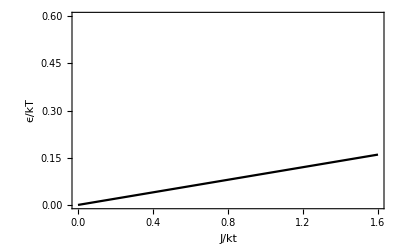

```mathematica
line=Plot[0.1x,{x,0,1.6},Frame->True,PlotStyle->Black,PlotRange->{0,0.6},FrameLabel->{"J/kt","ϵ/kT"}]
```

```mathematica
(* 1 = 1 peak at 0; 2 = 1 peak at L; 3 = 1 peak other; 4 = 2 peaks, first larger; 5 = 2 peaks, second larger *)
```

```mathematica
1.5/0.02+1
```

76.

```mathematica
0.08/0.02+1
```

5.

```mathematica
legend=SwatchLegend["Rainbow",{"One peak at N=0","One peak at N=L","One peak elsewhere","Two peaks, first larger","Two peaks, second larger"}]
```

```mathematica
mapShort
```

{{0.,0.,3},{0.,0.02,3},{0.,0.04,3},{0.,0.06,3},{0.,0.08,3},{0.,0.1,3},{0.,0.12,3},{0.,0.14,3},{0.,0.16,3},{0.,0.18,3},{0.,0.2,3},{0.,0.22,1},{0.,0.24,1},{0.,0.26,1},{0.,0.28,1},{0.,0.3,1},{0.,0.32,1},{0.,0.34,1},{0.,0.36,1},{0.,0.38,1},{0.,0.4,1},{0.,0.42,1},{0.,0.44,1},{0.,0.46,1},{0.,0.48,1},{0.,0.5,1},{0.,0.52,1},{0.,0.54,1},{0.,0.56,1},{0.,0.58,1},{0.,0.6,1},{0.02,0.,3},{0.02,0.02,3},{0.02,0.04,3},{0.02,0.06,3},{0.02,0.08,3},{0.02,0.1,3},{0.02,0.12,3},{0.02,0.14,3},{0.02,0.16,3},{0.02,0.18,3},{0.02,0.2,1},{0.02,0.22,1},{0.02,0.24,1},{0.02,0.26,1},{0.02,0.28,1},{0.02,0.3,1},{0.02,0.32,1},{0.02,0.34,1},{0.02,0.36,1},{0.02,0.38,1},{0.02,0.4,1},{0.02,0.42,1},{0.02,0.44,1},{0.02,0.46,1},{0.02,0.48,1},{0.02,0.5,1},{0.02,0.52,1},{0.02,0.54,1},{0.02,0.56,1},{0.02,0.58,1},{0.02,0.6,1},{0.04,0.,3},{0.04,0.02,3},{0.04,0.04,3},{0.04,0.06,3},{0.04,0.08,3},{0.04,0.1,3},{0.04,0.12,3},{0.04,0.14,3},{0.04,0.16,3},{0.04,0.18,3},{0.04,0.2,1},{0.04,0.22,1},{0.04,0.24,1},{0.04,0.26,1},{0.04,0.28,1},{0.04,0.3,1},{0.04,0.32,1},{0.04,0.34,1},{0.04,0.36,1},{0.04,0.38,1},{0.04,0.4,1},{0.04,0.42,1},{0.04,0.44,1},{0.04,0.46,1},{0.04,0.48,1},{0.04,0.5,1},{0.04,0.52,1},{0.04,0.54,1},{0.04,0.56,1},{0.04,0.58,1},{0.04,0.6,1},{0.06,0.,3},{0.06,0.02,3},{0.06,0.04,3},{0.06,0.06,3},{0.06,0.08,3},{0.06,0.1,3},{0.06,0.12,3},{0.06,0.14,3},{0.06,0.16,3},{0.06,0.18,3},{0.06,0.2,1},{0.06,0.22,1},{0.06,0.24,1},{0.06,0.26,1},{0.06,0.28,1},{0.06,0.3,1},{0.06,0.32,1},{0.06,0.34,1},{0.06,0.36,1},{0.06,0.38,1},{0.06,0.4,1},{0.06,0.42,1},{0.06,0.44,1},{0.06,0.46,1},{0.06,0.48,1},{0.06,0.5,1},{0.06,0.52,1},{0.06,0.54,1},{0.06,0.56,1},{0.06,0.58,1},{0.06,0.6,1},{0.08,0.,3},{0.08,0.02,3},{0.08,0.04,3},{0.08,0.06,3},{0.08,0.08,3},{0.08,0.1,3},{0.08,0.12,3},{0.08,0.14,3},{0.08,0.16,3},{0.08,0.18,1},{0.08,0.2,1},{0.08,0.22,1},{0.08,0.24,1},{0.08,0.26,1},{0.08,0.28,1},{0.08,0.3,1},{0.08,0.32,1},{0.08,0.34,1},{0.08,0.36,1},{0.08,0.38,1},{0.08,0.4,1},{0.08,0.42,1},{0.08,0.44,1},{0.08,0.46,1},{0.08,0.48,1},{0.08,0.5,1},{0.08,0.52,1},{0.08,0.54,1},{0.08,0.56,1},{0.08,0.58,1},{0.08,0.6,1},{0.1,0.,3},{0.1,0.02,3},{0.1,0.04,3},{0.1,0.06,3},{0.1,0.08,3},{0.1,0.1,3},{0.1,0.12,3},{0.1,0.14,3},{0.1,0.16,3},{0.1,0.18,1},{0.1,0.2,1},{0.1,0.22,1},{0.1,0.24,1},{0.1,0.26,1},{0.1,0.28,1},{0.1,0.3,1},{0.1,0.32,1},{0.1,0.34,1},{0.1,0.36,1},{0.1,0.38,1},{0.1,0.4,1},{0.1,0.42,1},{0.1,0.44,1},{0.1,0.46,1},{0.1,0.48,1},{0.1,0.5,1},{0.1,0.52,1},{0.1,0.54,1},{0.1,0.56,1},{0.1,0.58,1},{0.1,0.6,1},{0.12,0.,3},{0.12,0.02,3},{0.12,0.04,3},{0.12,0.06,3},{0.12,0.08,3},{0.12,0.1,3},{0.12,0.12,3},{0.12,0.14,3},{0.12,0.16,3},{0.12,0.18,1},{0.12,0.2,1},{0.12,0.22,1},{0.12,0.24,1},{0.12,0.26,1},{0.12,0.28,1},{0.12,0.3,1},{0.12,0.32,1},{0.12,0.34,1},{0.12,0.36,1},{0.12,0.38,1},{0.12,0.4,1},{0.12,0.42,1},{0.12,0.44,1},{0.12,0.46,1},{0.12,0.48,1},{0.12,0.5,1},{0.12,0.52,1},{0.12,0.54,1},{0.12,0.56,1},{0.12,0.58,1},{0.12,0.6,1},{0.14,0.,3},{0.14,0.02,3},{0.14,0.04,3},{0.14,0.06,3},{0.14,0.08,3},{0.14,0.1,3},{0.14,0.12,3},{0.14,0.14,3},{0.14,0.16,3},{0.14,0.18,1},{0.14,0.2,1},{0.14,0.22,1},{0.14,0.24,1},{0.14,0.26,1},{0.14,0.28,1},{0.14,0.3,1},{0.14,0.32,1},{0.14,0.34,1},{0.14,0.36,1},{0.14,0.38,1},{0.14,0.4,1},{0.14,0.42,1},{0.14,0.44,1},{0.14,0.46,1},{0.14,0.48,1},{0.14,0.5,1},{0.14,0.52,1},{0.14,0.54,1},{0.14,0.56,1},{0.14,0.58,1},{0.14,0.6,1},{0.16,0.,3},{0.16,0.02,3},{0.16,0.04,3},{0.16,0.06,3},{0.16,0.08,3},{0.16,0.1,3},{0.16,0.12,3},{0.16,0.14,3},{0.16,0.16,1},{0.16,0.18,1},{0.16,0.2,1},{0.16,0.22,1},{0.16,0.24,1},{0.16,0.26,1},{0.16,0.28,1},{0.16,0.3,1},{0.16,0.32,1},{0.16,0.34,1},{0.16,0.36,1},{0.16,0.38,1},{0.16,0.4,1},{0.16,0.42,1},{0.16,0.44,1},{0.16,0.46,1},{0.16,0.48,1},{0.16,0.5,1},{0.16,0.52,1},{0.16,0.54,1},{0.16,0.56,1},{0.16,0.58,1},{0.16,0.6,1},{0.18,0.,3},{0.18,0.02,3},{0.18,0.04,3},{0.18,0.06,3},{0.18,0.08,3},{0.18,0.1,3},{0.18,0.12,3},{0.18,0.14,3},{0.18,0.16,1},{0.18,0.18,1},{0.18,0.2,1},{0.18,0.22,1},{0.18,0.24,1},{0.18,0.26,1},{0.18,0.28,1},{0.18,0.3,1},{0.18,0.32,1},{0.18,0.34,1},{0.18,0.36,1},{0.18,0.38,1},{0.18,0.4,1},{0.18,0.42,1},{0.18,0.44,1},{0.18,0.46,1},{0.18,0.48,1},{0.18,0.5,1},{0.18,0.52,1},{0.18,0.54,1},{0.18,0.56,1},{0.18,0.58,1},{0.18,0.6,1},{0.2,0.,3},{0.2,0.02,3},{0.2,0.04,3},{0.2,0.06,3},{0.2,0.08,3},{0.2,0.1,3},{0.2,0.12,3},{0.2,0.14,3},{0.2,0.16,1},{0.2,0.18,1},{0.2,0.2,1},{0.2,0.22,1},{0.2,0.24,1},{0.2,0.26,1},{0.2,0.28,1},{0.2,0.3,1},{0.2,0.32,1},{0.2,0.34,1},{0.2,0.36,1},{0.2,0.38,1},{0.2,0.4,1},{0.2,0.42,1},{0.2,0.44,1},{0.2,0.46,1},{0.2,0.48,1},{0.2,0.5,1},{0.2,0.52,1},{0.2,0.54,1},{0.2,0.56,1},{0.2,0.58,1},{0.2,0.6,1},{0.22,0.,3},{0.22,0.02,3},{0.22,0.04,3},{0.22,0.06,3},{0.22,0.08,3},{0.22,0.1,3},{0.22,0.12,3},{0.22,0.14,3},{0.22,0.16,1},{0.22,0.18,1},{0.22,0.2,1},{0.22,0.22,1},{0.22,0.24,1},{0.22,0.26,1},{0.22,0.28,1},{0.22,0.3,1},{0.22,0.32,1},{0.22,0.34,1},{0.22,0.36,1},{0.22,0.38,1},{0.22,0.4,1},{0.22,0.42,1},{0.22,0.44,1},{0.22,0.46,1},{0.22,0.48,1},{0.22,0.5,1},{0.22,0.52,1},{0.22,0.54,1},{0.22,0.56,1},{0.22,0.58,1},{0.22,0.6,1},{0.24,0.,3},{0.24,0.02,3},{0.24,0.04,3},{0.24,0.06,3},{0.24,0.08,3},{0.24,0.1,3},{0.24,0.12,3},{0.24,0.14,3},{0.24,0.16,1},{0.24,0.18,1},{0.24,0.2,1},{0.24,0.22,1},{0.24,0.24,1},{0.24,0.26,1},{0.24,0.28,1},{0.24,0.3,1},{0.24,0.32,1},{0.24,0.34,1},{0.24,0.36,1},{0.24,0.38,1},{0.24,0.4,1},{0.24,0.42,1},{0.24,0.44,1},{0.24,0.46,1},{0.24,0.48,1},{0.24,0.5,1},{0.24,0.52,1},{0.24,0.54,1},{0.24,0.56,1},{0.24,0.58,1},{0.24,0.6,1},{0.26,0.,3},{0.26,0.02,3},{0.26,0.04,3},{0.26,0.06,3},{0.26,0.08,3},{0.26,0.1,3},{0.26,0.12,3},{0.26,0.14,1},{0.26,0.16,1},{0.26,0.18,1},{0.26,0.2,1},{0.26,0.22,1},{0.26,0.24,1},{0.26,0.26,1},{0.26,0.28,1},{0.26,0.3,1},{0.26,0.32,1},{0.26,0.34,1},{0.26,0.36,1},{0.26,0.38,1},{0.26,0.4,1},{0.26,0.42,1},{0.26,0.44,1},{0.26,0.46,1},{0.26,0.48,1},{0.26,0.5,1},{0.26,0.52,1},{0.26,0.54,1},{0.26,0.56,1},{0.26,0.58,1},{0.26,0.6,1},{0.28,0.,3},{0.28,0.02,3},{0.28,0.04,3},{0.28,0.06,3},{0.28,0.08,3},{0.28,0.1,3},{0.28,0.12,3},{0.28,0.14,1},{0.28,0.16,1},{0.28,0.18,1},{0.28,0.2,1},{0.28,0.22,1},{0.28,0.24,1},{0.28,0.26,1},{0.28,0.28,1},{0.28,0.3,1},{0.28,0.32,1},{0.28,0.34,1},{0.28,0.36,1},{0.28,0.38,1},{0.28,0.4,1},{0.28,0.42,1},{0.28,0.44,1},{0.28,0.46,1},{0.28,0.48,1},{0.28,0.5,1},{0.28,0.52,1},{0.28,0.54,1},{0.28,0.56,1},{0.28,0.58,1},{0.28,0.6,1},{0.3,0.,3},{0.3,0.02,3},{0.3,0.04,3},{0.3,0.06,3},{0.3,0.08,3},{0.3,0.1,3},{0.3,0.12,3},{0.3,0.14,1},{0.3,0.16,1},{0.3,0.18,1},{0.3,0.2,1},{0.3,0.22,1},{0.3,0.24,1},{0.3,0.26,1},{0.3,0.28,1},{0.3,0.3,1},{0.3,0.32,1},{0.3,0.34,1},{0.3,0.36,1},{0.3,0.38,1},{0.3,0.4,1},{0.3,0.42,1},{0.3,0.44,1},{0.3,0.46,1},{0.3,0.48,1},{0.3,0.5,1},{0.3,0.52,1},{0.3,0.54,1},{0.3,0.56,1},{0.3,0.58,1},{0.3,0.6,1},{0.32,0.,3},{0.32,0.02,3},{0.32,0.04,3},{0.32,0.06,3},{0.32,0.08,3},{0.32,0.1,3},{0.32,0.12,3},{0.32,0.14,1},{0.32,0.16,1},{0.32,0.18,1},{0.32,0.2,1},{0.32,0.22,1},{0.32,0.24,1},{0.32,0.26,1},{0.32,0.28,1},{0.32,0.3,1},{0.32,0.32,1},{0.32,0.34,1},{0.32,0.36,1},{0.32,0.38,1},{0.32,0.4,1},{0.32,0.42,1},{0.32,0.44,1},{0.32,0.46,1},{0.32,0.48,1},{0.32,0.5,1},{0.32,0.52,1},{0.32,0.54,1},{0.32,0.56,1},{0.32,0.58,1},{0.32,0.6,1},{0.34,0.,3},{0.34,0.02,3},{0.34,0.04,3},{0.34,0.06,3},{0.34,0.08,3},{0.34,0.1,3},{0.34,0.12,3},{0.34,0.14,1},{0.34,0.16,1},{0.34,0.18,1},{0.34,0.2,1},{0.34,0.22,1},{0.34,0.24,1},{0.34,0.26,1},{0.34,0.28,1},{0.34,0.3,1},{0.34,0.32,1},{0.34,0.34,1},{0.34,0.36,1},{0.34,0.38,1},{0.34,0.4,1},{0.34,0.42,1},{0.34,0.44,1},{0.34,0.46,1},{0.34,0.48,1},{0.34,0.5,1},{0.34,0.52,1},{0.34,0.54,1},{0.34,0.56,1},{0.34,0.58,1},{0.34,0.6,1},{0.36,0.,3},{0.36,0.02,3},{0.36,0.04,3},{0.36,0.06,3},{0.36,0.08,3},{0.36,0.1,3},{0.36,0.12,3},{0.36,0.14,1},{0.36,0.16,1},{0.36,0.18,1},{0.36,0.2,1},{0.36,0.22,1},{0.36,0.24,1},{0.36,0.26,1},{0.36,0.28,1},{0.36,0.3,1},{0.36,0.32,1},{0.36,0.34,1},{0.36,0.36,1},{0.36,0.38,1},{0.36,0.4,1},{0.36,0.42,1},{0.36,0.44,1},{0.36,0.46,1},{0.36,0.48,1},{0.36,0.5,1},{0.36,0.52,1},{0.36,0.54,1},{0.36,0.56,1},{0.36,0.58,1},{0.36,0.6,1},{0.38,0.,3},{0.38,0.02,3},{0.38,0.04,3},{0.38,0.06,3},{0.38,0.08,3},{0.38,0.1,3},{0.38,0.12,3},{0.38,0.14,1},{0.38,0.16,1},{0.38,0.18,1},{0.38,0.2,1},{0.38,0.22,1},{0.38,0.24,1},{0.38,0.26,1},{0.38,0.28,1},{0.38,0.3,1},{0.38,0.32,1},{0.38,0.34,1},{0.38,0.36,1},{0.38,0.38,1},{0.38,0.4,1},{0.38,0.42,1},{0.38,0.44,1},{0.38,0.46,1},{0.38,0.48,1},{0.38,0.5,1},{0.38,0.52,1},{0.38,0.54,1},{0.38,0.56,1},{0.38,0.58,1},{0.38,0.6,1},{0.4,0.,3},{0.4,0.02,3},{0.4,0.04,3},{0.4,0.06,3},{0.4,0.08,3},{0.4,0.1,3},{0.4,0.12,1},{0.4,0.14,1},{0.4,0.16,1},{0.4,0.18,1},{0.4,0.2,1},{0.4,0.22,1},{0.4,0.24,1},{0.4,0.26,1},{0.4,0.28,1},{0.4,0.3,1},{0.4,0.32,1},{0.4,0.34,1},{0.4,0.36,1},{0.4,0.38,1},{0.4,0.4,1},{0.4,0.42,1},{0.4,0.44,1},{0.4,0.46,1},{0.4,0.48,1},{0.4,0.5,1},{0.4,0.52,1},{0.4,0.54,1},{0.4,0.56,1},{0.4,0.58,1},{0.4,0.6,1},{0.42,0.,2},{0.42,0.02,3},{0.42,0.04,3},{0.42,0.06,3},{0.42,0.08,3},{0.42,0.1,3},{0.42,0.12,1},{0.42,0.14,1},{0.42,0.16,1},{0.42,0.18,1},{0.42,0.2,1},{0.42,0.22,1},{0.42,0.24,1},{0.42,0.26,1},{0.42,0.28,1},{0.42,0.3,1},{0.42,0.32,1},{0.42,0.34,1},{0.42,0.36,1},{0.42,0.38,1},{0.42,0.4,1},{0.42,0.42,1},{0.42,0.44,1},{0.42,0.46,1},{0.42,0.48,1},{0.42,0.5,1},{0.42,0.52,1},{0.42,0.54,1},{0.42,0.56,1},{0.42,0.58,1},{0.42,0.6,1},{0.44,0.,2},{0.44,0.02,3},{0.44,0.04,3},{0.44,0.06,3},{0.44,0.08,3},{0.44,0.1,3},{0.44,0.12,1},{0.44,0.14,1},{0.44,0.16,1},{0.44,0.18,1},{0.44,0.2,1},{0.44,0.22,1},{0.44,0.24,1},{0.44,0.26,1},{0.44,0.28,1},{0.44,0.3,1},{0.44,0.32,1},{0.44,0.34,1},{0.44,0.36,1},{0.44,0.38,1},{0.44,0.4,1},{0.44,0.42,1},{0.44,0.44,1},{0.44,0.46,1},{0.44,0.48,1},{0.44,0.5,1},{0.44,0.52,1},{0.44,0.54,1},{0.44,0.56,1},{0.44,0.58,1},{0.44,0.6,1},{0.46,0.,2},{0.46,0.02,4},{0.46,0.04,3},{0.46,0.06,3},{0.46,0.08,3},{0.46,0.1,3},{0.46,0.12,1},{0.46,0.14,1},{0.46,0.16,1},{0.46,0.18,1},{0.46,0.2,1},{0.46,0.22,1},{0.46,0.24,1},{0.46,0.26,1},{0.46,0.28,1},{0.46,0.3,1},{0.46,0.32,1},{0.46,0.34,1},{0.46,0.36,1},{0.46,0.38,1},{0.46,0.4,1},{0.46,0.42,1},{0.46,0.44,1},{0.46,0.46,1},{0.46,0.48,1},{0.46,0.5,1},{0.46,0.52,1},{0.46,0.54,1},{0.46,0.56,1},{0.46,0.58,1},{0.46,0.6,1},{0.48,0.,2},{0.48,0.02,5},{0.48,0.04,3},{0.48,0.06,3},{0.48,0.08,3},{0.48,0.1,3},{0.48,0.12,1},{0.48,0.14,1},{0.48,0.16,1},{0.48,0.18,1},{0.48,0.2,1},{0.48,0.22,1},{0.48,0.24,1},{0.48,0.26,1},{0.48,0.28,1},{0.48,0.3,1},{0.48,0.32,1},{0.48,0.34,1},{0.48,0.36,1},{0.48,0.38,1},{0.48,0.4,1},{0.48,0.42,1},{0.48,0.44,1},{0.48,0.46,1},{0.48,0.48,1},{0.48,0.5,1},{0.48,0.52,1},{0.48,0.54,1},{0.48,0.56,1},{0.48,0.58,1},{0.48,0.6,1},{0.5,0.,2},{0.5,0.02,5},{0.5,0.04,4},{0.5,0.06,3},{0.5,0.08,3},{0.5,0.1,3},{0.5,0.12,1},{0.5,0.14,1},{0.5,0.16,1},{0.5,0.18,1},{0.5,0.2,1},{0.5,0.22,1},{0.5,0.24,1},{0.5,0.26,1},{0.5,0.28,1},{0.5,0.3,1},{0.5,0.32,1},{0.5,0.34,1},{0.5,0.36,1},{0.5,0.38,1},{0.5,0.4,1},{0.5,0.42,1},{0.5,0.44,1},{0.5,0.46,1},{0.5,0.48,1},{0.5,0.5,1},{0.5,0.52,1},{0.5,0.54,1},{0.5,0.56,1},{0.5,0.58,1},{0.5,0.6,1},{0.52,0.,2},{0.52,0.02,5},{0.52,0.04,4},{0.52,0.06,3},{0.52,0.08,3},{0.52,0.1,3},{0.52,0.12,1},{0.52,0.14,1},{0.52,0.16,1},{0.52,0.18,1},{0.52,0.2,1},{0.52,0.22,1},{0.52,0.24,1},{0.52,0.26,1},{0.52,0.28,1},{0.52,0.3,1},{0.52,0.32,1},{0.52,0.34,1},{0.52,0.36,1},{0.52,0.38,1},{0.52,0.4,1},{0.52,0.42,1},{0.52,0.44,1},{0.52,0.46,1},{0.52,0.48,1},{0.52,0.5,1},{0.52,0.52,1},{0.52,0.54,1},{0.52,0.56,1},{0.52,0.58,1},{0.52,0.6,1},{0.54,0.,2},{0.54,0.02,2},{0.54,0.04,4},{0.54,0.06,3},{0.54,0.08,3},{0.54,0.1,3},{0.54,0.12,1},{0.54,0.14,1},{0.54,0.16,1},{0.54,0.18,1},{0.54,0.2,1},{0.54,0.22,1},{0.54,0.24,1},{0.54,0.26,1},{0.54,0.28,1},{0.54,0.3,1},{0.54,0.32,1},{0.54,0.34,1},{0.54,0.36,1},{0.54,0.38,1},{0.54,0.4,1},{0.54,0.42,1},{0.54,0.44,1},{0.54,0.46,1},{0.54,0.48,1},{0.54,0.5,1},{0.54,0.52,1},{0.54,0.54,1},{0.54,0.56,1},{0.54,0.58,1},{0.54,0.6,1},{0.56,0.,2},{0.56,0.02,2},{0.56,0.04,4},{0.56,0.06,4},{0.56,0.08,3},{0.56,0.1,3},{0.56,0.12,1},{0.56,0.14,1},{0.56,0.16,1},{0.56,0.18,1},{0.56,0.2,1},{0.56,0.22,1},{0.56,0.24,1},{0.56,0.26,1},{0.56,0.28,1},{0.56,0.3,1},{0.56,0.32,1},{0.56,0.34,1},{0.56,0.36,1},{0.56,0.38,1},{0.56,0.4,1},{0.56,0.42,1},{0.56,0.44,1},{0.56,0.46,1},{0.56,0.48,1},{0.56,0.5,1},{0.56,0.52,1},{0.56,0.54,1},{0.56,0.56,1},{0.56,0.58,1},{0.56,0.6,1},{0.58,0.,2},{0.58,0.02,2},{0.58,0.04,5},{0.58,0.06,4},{0.58,0.08,3},{0.58,0.1,3},{0.58,0.12,1},{0.58,0.14,1},{0.58,0.16,1},{0.58,0.18,1},{0.58,0.2,1},{0.58,0.22,1},{0.58,0.24,1},{0.58,0.26,1},{0.58,0.28,1},{0.58,0.3,1},{0.58,0.32,1},{0.58,0.34,1},{0.58,0.36,1},{0.58,0.38,1},{0.58,0.4,1},{0.58,0.42,1},{0.58,0.44,1},{0.58,0.46,1},{0.58,0.48,1},{0.58,0.5,1},{0.58,0.52,1},{0.58,0.54,1},{0.58,0.56,1},{0.58,0.58,1},{0.58,0.6,1},{0.6,0.,2},{0.6,0.02,2},{0.6,0.04,5},{0.6,0.06,4},{0.6,0.08,3},{0.6,0.1,3},{0.6,0.12,1},{0.6,0.14,1},{0.6,0.16,1},{0.6,0.18,1},{0.6,0.2,1},{0.6,0.22,1},{0.6,0.24,1},{0.6,0.26,1},{0.6,0.28,1},{0.6,0.3,1},{0.6,0.32,1},{0.6,0.34,1},{0.6,0.36,1},{0.6,0.38,1},{0.6,0.4,1},{0.6,0.42,1},{0.6,0.44,1},{0.6,0.46,1},{0.6,0.48,1},{0.6,0.5,1},{0.6,0.52,1},{0.6,0.54,1},{0.6,0.56,1},{0.6,0.58,1},{0.6,0.6,1},{0.62,0.,2},{0.62,0.02,2},{0.62,0.04,5},{0.62,0.06,4},{0.62,0.08,4},{0.62,0.1,3},{0.62,0.12,1},{0.62,0.14,1},{0.62,0.16,1},{0.62,0.18,1},{0.62,0.2,1},{0.62,0.22,1},{0.62,0.24,1},{0.62,0.26,1},{0.62,0.28,1},{0.62,0.3,1},{0.62,0.32,1},{0.62,0.34,1},{0.62,0.36,1},{0.62,0.38,1},{0.62,0.4,1},{0.62,0.42,1},{0.62,0.44,1},{0.62,0.46,1},{0.62,0.48,1},{0.62,0.5,1},{0.62,0.52,1},{0.62,0.54,1},{0.62,0.56,1},{0.62,0.58,1},{0.62,0.6,1},{0.64,0.,2},{0.64,0.02,2},{0.64,0.04,5},{0.64,0.06,4},{0.64,0.08,4},{0.64,0.1,3},{0.64,0.12,1},{0.64,0.14,1},{0.64,0.16,1},{0.64,0.18,1},{0.64,0.2,1},{0.64,0.22,1},{0.64,0.24,1},{0.64,0.26,1},{0.64,0.28,1},{0.64,0.3,1},{0.64,0.32,1},{0.64,0.34,1},{0.64,0.36,1},{0.64,0.38,1},{0.64,0.4,1},{0.64,0.42,1},{0.64,0.44,1},{0.64,0.46,1},{0.64,0.48,1},{0.64,0.5,1},{0.64,0.52,1},{0.64,0.54,1},{0.64,0.56,1},{0.64,0.58,1},{0.64,0.6,1},{0.66,0.,2},{0.66,0.02,2},{0.66,0.04,5},{0.66,0.06,4},{0.66,0.08,4},{0.66,0.1,4},{0.66,0.12,1},{0.66,0.14,1},{0.66,0.16,1},{0.66,0.18,1},{0.66,0.2,1},{0.66,0.22,1},{0.66,0.24,1},{0.66,0.26,1},{0.66,0.28,1},{0.66,0.3,1},{0.66,0.32,1},{0.66,0.34,1},{0.66,0.36,1},{0.66,0.38,1},{0.66,0.4,1},{0.66,0.42,1},{0.66,0.44,1},{0.66,0.46,1},{0.66,0.48,1},{0.66,0.5,1},{0.66,0.52,1},{0.66,0.54,1},{0.66,0.56,1},{0.66,0.58,1},{0.66,0.6,1},{0.68,0.,2},{0.68,0.02,2},{0.68,0.04,5},{0.68,0.06,5},{0.68,0.08,4},{0.68,0.1,4},{0.68,0.12,1},{0.68,0.14,1},{0.68,0.16,1},{0.68,0.18,1},{0.68,0.2,1},{0.68,0.22,1},{0.68,0.24,1},{0.68,0.26,1},{0.68,0.28,1},{0.68,0.3,1},{0.68,0.32,1},{0.68,0.34,1},{0.68,0.36,1},{0.68,0.38,1},{0.68,0.4,1},{0.68,0.42,1},{0.68,0.44,1},{0.68,0.46,1},{0.68,0.48,1},{0.68,0.5,1},{0.68,0.52,1},{0.68,0.54,1},{0.68,0.56,1},{0.68,0.58,1},{0.68,0.6,1},{0.7,0.,2},{0.7,0.02,2},{0.7,0.04,5},{0.7,0.06,5},{0.7,0.08,4},{0.7,0.1,4},{0.7,0.12,1},{0.7,0.14,1},{0.7,0.16,1},{0.7,0.18,1},{0.7,0.2,1},{0.7,0.22,1},{0.7,0.24,1},{0.7,0.26,1},{0.7,0.28,1},{0.7,0.3,1},{0.7,0.32,1},{0.7,0.34,1},{0.7,0.36,1},{0.7,0.38,1},{0.7,0.4,1},{0.7,0.42,1},{0.7,0.44,1},{0.7,0.46,1},{0.7,0.48,1},{0.7,0.5,1},{0.7,0.52,1},{0.7,0.54,1},{0.7,0.56,1},{0.7,0.58,1},{0.7,0.6,1},{0.72,0.,2},{0.72,0.02,2},{0.72,0.04,5},{0.72,0.06,5},{0.72,0.08,4},{0.72,0.1,4},{0.72,0.12,4},{0.72,0.14,1},{0.72,0.16,1},{0.72,0.18,1},{0.72,0.2,1},{0.72,0.22,1},{0.72,0.24,1},{0.72,0.26,1},{0.72,0.28,1},{0.72,0.3,1},{0.72,0.32,1},{0.72,0.34,1},{0.72,0.36,1},{0.72,0.38,1},{0.72,0.4,1},{0.72,0.42,1},{0.72,0.44,1},{0.72,0.46,1},{0.72,0.48,1},{0.72,0.5,1},{0.72,0.52,1},{0.72,0.54,1},{0.72,0.56,1},{0.72,0.58,1},{0.72,0.6,1},{0.74,0.,2},{0.74,0.02,2},{0.74,0.04,5},{0.74,0.06,5},{0.74,0.08,4},{0.74,0.1,4},{0.74,0.12,4},{0.74,0.14,1},{0.74,0.16,1},{0.74,0.18,1},{0.74,0.2,1},{0.74,0.22,1},{0.74,0.24,1},{0.74,0.26,1},{0.74,0.28,1},{0.74,0.3,1},{0.74,0.32,1},{0.74,0.34,1},{0.74,0.36,1},{0.74,0.38,1},{0.74,0.4,1},{0.74,0.42,1},{0.74,0.44,1},{0.74,0.46,1},{0.74,0.48,1},{0.74,0.5,1},{0.74,0.52,1},{0.74,0.54,1},{0.74,0.56,1},{0.74,0.58,1},{0.74,0.6,1},{0.76,0.,2},{0.76,0.02,2},{0.76,0.04,5},{0.76,0.06,5},{0.76,0.08,4},{0.76,0.1,4},{0.76,0.12,4},{0.76,0.14,1},{0.76,0.16,1},{0.76,0.18,1},{0.76,0.2,1},{0.76,0.22,1},{0.76,0.24,1},{0.76,0.26,1},{0.76,0.28,1},{0.76,0.3,1},{0.76,0.32,1},{0.76,0.34,1},{0.76,0.36,1},{0.76,0.38,1},{0.76,0.4,1},{0.76,0.42,1},{0.76,0.44,1},{0.76,0.46,1},{0.76,0.48,1},{0.76,0.5,1},{0.76,0.52,1},{0.76,0.54,1},{0.76,0.56,1},{0.76,0.58,1},{0.76,0.6,1},{0.78,0.,2},{0.78,0.02,2},{0.78,0.04,5},{0.78,0.06,5},{0.78,0.08,4},{0.78,0.1,4},{0.78,0.12,4},{0.78,0.14,4},{0.78,0.16,1},{0.78,0.18,1},{0.78,0.2,1},{0.78,0.22,1},{0.78,0.24,1},{0.78,0.26,1},{0.78,0.28,1},{0.78,0.3,1},{0.78,0.32,1},{0.78,0.34,1},{0.78,0.36,1},{0.78,0.38,1},{0.78,0.4,1},{0.78,0.42,1},{0.78,0.44,1},{0.78,0.46,1},{0.78,0.48,1},{0.78,0.5,1},{0.78,0.52,1},{0.78,0.54,1},{0.78,0.56,1},{0.78,0.58,1},{0.78,0.6,1},{0.8,0.,2},{0.8,0.02,2},{0.8,0.04,5},{0.8,0.06,5},{0.8,0.08,4},{0.8,0.1,4},{0.8,0.12,4},{0.8,0.14,4},{0.8,0.16,1},{0.8,0.18,1},{0.8,0.2,1},{0.8,0.22,1},{0.8,0.24,1},{0.8,0.26,1},{0.8,0.28,1},{0.8,0.3,1},{0.8,0.32,1},{0.8,0.34,1},{0.8,0.36,1},{0.8,0.38,1},{0.8,0.4,1},{0.8,0.42,1},{0.8,0.44,1},{0.8,0.46,1},{0.8,0.48,1},{0.8,0.5,1},{0.8,0.52,1},{0.8,0.54,1},{0.8,0.56,1},{0.8,0.58,1},{0.8,0.6,1},{0.82,0.,2},{0.82,0.02,2},{0.82,0.04,5},{0.82,0.06,5},{0.82,0.08,4},{0.82,0.1,4},{0.82,0.12,4},{0.82,0.14,4},{0.82,0.16,1},{0.82,0.18,1},{0.82,0.2,1},{0.82,0.22,1},{0.82,0.24,1},{0.82,0.26,1},{0.82,0.28,1},{0.82,0.3,1},{0.82,0.32,1},{0.82,0.34,1},{0.82,0.36,1},{0.82,0.38,1},{0.82,0.4,1},{0.82,0.42,1},{0.82,0.44,1},{0.82,0.46,1},{0.82,0.48,1},{0.82,0.5,1},{0.82,0.52,1},{0.82,0.54,1},{0.82,0.56,1},{0.82,0.58,1},{0.82,0.6,1},{0.84,0.,2},{0.84,0.02,2},{0.84,0.04,5},{0.84,0.06,5},{0.84,0.08,5},{0.84,0.1,4},{0.84,0.12,4},{0.84,0.14,4},{0.84,0.16,4},{0.84,0.18,1},{0.84,0.2,1},{0.84,0.22,1},{0.84,0.24,1},{0.84,0.26,1},{0.84,0.28,1},{0.84,0.3,1},{0.84,0.32,1},{0.84,0.34,1},{0.84,0.36,1},{0.84,0.38,1},{0.84,0.4,1},{0.84,0.42,1},{0.84,0.44,1},{0.84,0.46,1},{0.84,0.48,1},{0.84,0.5,1},{0.84,0.52,1},{0.84,0.54,1},{0.84,0.56,1},{0.84,0.58,1},{0.84,0.6,1},{0.86,0.,2},{0.86,0.02,2},{0.86,0.04,2},{0.86,0.06,5},{0.86,0.08,5},{0.86,0.1,4},{0.86,0.12,4},{0.86,0.14,4},{0.86,0.16,4},{0.86,0.18,1},{0.86,0.2,1},{0.86,0.22,1},{0.86,0.24,1},{0.86,0.26,1},{0.86,0.28,1},{0.86,0.3,1},{0.86,0.32,1},{0.86,0.34,1},{0.86,0.36,1},{0.86,0.38,1},{0.86,0.4,1},{0.86,0.42,1},{0.86,0.44,1},{0.86,0.46,1},{0.86,0.48,1},{0.86,0.5,1},{0.86,0.52,1},{0.86,0.54,1},{0.86,0.56,1},{0.86,0.58,1},{0.86,0.6,1},{0.88,0.,2},{0.88,0.02,2},{0.88,0.04,2},{0.88,0.06,5},{0.88,0.08,5},{0.88,0.1,4},{0.88,0.12,4},{0.88,0.14,4},{0.88,0.16,4},{0.88,0.18,1},{0.88,0.2,1},{0.88,0.22,1},{0.88,0.24,1},{0.88,0.26,1},{0.88,0.28,1},{0.88,0.3,1},{0.88,0.32,1},{0.88,0.34,1},{0.88,0.36,1},{0.88,0.38,1},{0.88,0.4,1},{0.88,0.42,1},{0.88,0.44,1},{0.88,0.46,1},{0.88,0.48,1},{0.88,0.5,1},{0.88,0.52,1},{0.88,0.54,1},{0.88,0.56,1},{0.88,0.58,1},{0.88,0.6,1},{0.9,0.,2},{0.9,0.02,2},{0.9,0.04,2},{0.9,0.06,5},{0.9,0.08,5},{0.9,0.1,4},{0.9,0.12,4},{0.9,0.14,4},{0.9,0.16,4},{0.9,0.18,4},{0.9,0.2,1},{0.9,0.22,1},{0.9,0.24,1},{0.9,0.26,1},{0.9,0.28,1},{0.9,0.3,1},{0.9,0.32,1},{0.9,0.34,1},{0.9,0.36,1},{0.9,0.38,1},{0.9,0.4,1},{0.9,0.42,1},{0.9,0.44,1},{0.9,0.46,1},{0.9,0.48,1},{0.9,0.5,1},{0.9,0.52,1},{0.9,0.54,1},{0.9,0.56,1},{0.9,0.58,1},{0.9,0.6,1},{0.92,0.,2},{0.92,0.02,2},{0.92,0.04,2},{0.92,0.06,5},{0.92,0.08,5},{0.92,0.1,4},{0.92,0.12,4},{0.92,0.14,4},{0.92,0.16,4},{0.92,0.18,4},{0.92,0.2,1},{0.92,0.22,1},{0.92,0.24,1},{0.92,0.26,1},{0.92,0.28,1},{0.92,0.3,1},{0.92,0.32,1},{0.92,0.34,1},{0.92,0.36,1},{0.92,0.38,1},{0.92,0.4,1},{0.92,0.42,1},{0.92,0.44,1},{0.92,0.46,1},{0.92,0.48,1},{0.92,0.5,1},{0.92,0.52,1},{0.92,0.54,1},{0.92,0.56,1},{0.92,0.58,1},{0.92,0.6,1},{0.94,0.,2},{0.94,0.02,2},{0.94,0.04,2},{0.94,0.06,5},{0.94,0.08,5},{0.94,0.1,4},{0.94,0.12,4},{0.94,0.14,4},{0.94,0.16,4},{0.94,0.18,4},{0.94,0.2,1},{0.94,0.22,1},{0.94,0.24,1},{0.94,0.26,1},{0.94,0.28,1},{0.94,0.3,1},{0.94,0.32,1},{0.94,0.34,1},{0.94,0.36,1},{0.94,0.38,1},{0.94,0.4,1},{0.94,0.42,1},{0.94,0.44,1},{0.94,0.46,1},{0.94,0.48,1},{0.94,0.5,1},{0.94,0.52,1},{0.94,0.54,1},{0.94,0.56,1},{0.94,0.58,1},{0.94,0.6,1},{0.96,0.,2},{0.96,0.02,2},{0.96,0.04,2},{0.96,0.06,5},{0.96,0.08,5},{0.96,0.1,4},{0.96,0.12,4},{0.96,0.14,4},{0.96,0.16,4},{0.96,0.18,4},{0.96,0.2,1},{0.96,0.22,1},{0.96,0.24,1},{0.96,0.26,1},{0.96,0.28,1},{0.96,0.3,1},{0.96,0.32,1},{0.96,0.34,1},{0.96,0.36,1},{0.96,0.38,1},{0.96,0.4,1},{0.96,0.42,1},{0.96,0.44,1},{0.96,0.46,1},{0.96,0.48,1},{0.96,0.5,1},{0.96,0.52,1},{0.96,0.54,1},{0.96,0.56,1},{0.96,0.58,1},{0.96,0.6,1},{0.98,0.,2},{0.98,0.02,2},{0.98,0.04,2},{0.98,0.06,5},{0.98,0.08,5},{0.98,0.1,4},{0.98,0.12,4},{0.98,0.14,4},{0.98,0.16,4},{0.98,0.18,4},{0.98,0.2,4},{0.98,0.22,1},{0.98,0.24,1},{0.98,0.26,1},{0.98,0.28,1},{0.98,0.3,1},{0.98,0.32,1},{0.98,0.34,1},{0.98,0.36,1},{0.98,0.38,1},{0.98,0.4,1},{0.98,0.42,1},{0.98,0.44,1},{0.98,0.46,1},{0.98,0.48,1},{0.98,0.5,1},{0.98,0.52,1},{0.98,0.54,1},{0.98,0.56,1},{0.98,0.58,1},{0.98,0.6,1},{1.,0.,2},{1.,0.02,2},{1.,0.04,2},{1.,0.06,5},{1.,0.08,5},{1.,0.1,6},{1.,0.12,4},{1.,0.14,4},{1.,0.16,4},{1.,0.18,4},{1.,0.2,4},{1.,0.22,1},{1.,0.24,1},{1.,0.26,1},{1.,0.28,1},{1.,0.3,1},{1.,0.32,1},{1.,0.34,1},{1.,0.36,1},{1.,0.38,1},{1.,0.4,1},{1.,0.42,1},{1.,0.44,1},{1.,0.46,1},{1.,0.48,1},{1.,0.5,1},{1.,0.52,1},{1.,0.54,1},{1.,0.56,1},{1.,0.58,1},{1.,0.6,1},{1.02,0.,2},{1.02,0.02,2},{1.02,0.04,2},{1.02,0.06,5},{1.02,0.08,5},{1.02,0.1,5},{1.02,0.12,4},{1.02,0.14,4},{1.02,0.16,4},{1.02,0.18,4},{1.02,0.2,4},{1.02,0.22,1},{1.02,0.24,1},{1.02,0.26,1},{1.02,0.28,1},{1.02,0.3,1},{1.02,0.32,1},{1.02,0.34,1},{1.02,0.36,1},{1.02,0.38,1},{1.02,0.4,1},{1.02,0.42,1},{1.02,0.44,1},{1.02,0.46,1},{1.02,0.48,1},{1.02,0.5,1},{1.02,0.52,1},{1.02,0.54,1},{1.02,0.56,1},{1.02,0.58,1},{1.02,0.6,1},{1.04,0.,2},{1.04,0.02,2},{1.04,0.04,2},{1.04,0.06,5},{1.04,0.08,5},{1.04,0.1,5},{1.04,0.12,4},{1.04,0.14,4},{1.04,0.16,4},{1.04,0.18,4},{1.04,0.2,4},{1.04,0.22,4},{1.04,0.24,1},{1.04,0.26,1},{1.04,0.28,1},{1.04,0.3,1},{1.04,0.32,1},{1.04,0.34,1},{1.04,0.36,1},{1.04,0.38,1},{1.04,0.4,1},{1.04,0.42,1},{1.04,0.44,1},{1.04,0.46,1},{1.04,0.48,1},{1.04,0.5,1},{1.04,0.52,1},{1.04,0.54,1},{1.04,0.56,1},{1.04,0.58,1},{1.04,0.6,1},{1.06,0.,2},{1.06,0.02,2},{1.06,0.04,2},{1.06,0.06,5},{1.06,0.08,5},{1.06,0.1,5},{1.06,0.12,4},{1.06,0.14,4},{1.06,0.16,4},{1.06,0.18,4},{1.06,0.2,4},{1.06,0.22,4},{1.06,0.24,1},{1.06,0.26,1},{1.06,0.28,1},{1.06,0.3,1},{1.06,0.32,1},{1.06,0.34,1},{1.06,0.36,1},{1.06,0.38,1},{1.06,0.4,1},{1.06,0.42,1},{1.06,0.44,1},{1.06,0.46,1},{1.06,0.48,1},{1.06,0.5,1},{1.06,0.52,1},{1.06,0.54,1},{1.06,0.56,1},{1.06,0.58,1},{1.06,0.6,1},{1.08,0.,2},{1.08,0.02,2},{1.08,0.04,2},{1.08,0.06,5},{1.08,0.08,5},{1.08,0.1,5},{1.08,0.12,4},{1.08,0.14,4},{1.08,0.16,4},{1.08,0.18,4},{1.08,0.2,4},{1.08,0.22,4},{1.08,0.24,1},{1.08,0.26,1},{1.08,0.28,1},{1.08,0.3,1},{1.08,0.32,1},{1.08,0.34,1},{1.08,0.36,1},{1.08,0.38,1},{1.08,0.4,1},{1.08,0.42,1},{1.08,0.44,1},{1.08,0.46,1},{1.08,0.48,1},{1.08,0.5,1},{1.08,0.52,1},{1.08,0.54,1},{1.08,0.56,1},{1.08,0.58,1},{1.08,0.6,1},{1.1,0.,2},{1.1,0.02,2},{1.1,0.04,2},{1.1,0.06,5},{1.1,0.08,5},{1.1,0.1,5},{1.1,0.12,4},{1.1,0.14,4},{1.1,0.16,4},{1.1,0.18,4},{1.1,0.2,4},{1.1,0.22,4},{1.1,0.24,1},{1.1,0.26,1},{1.1,0.28,1},{1.1,0.3,1},{1.1,0.32,1},{1.1,0.34,1},{1.1,0.36,1},{1.1,0.38,1},{1.1,0.4,1},{1.1,0.42,1},{1.1,0.44,1},{1.1,0.46,1},{1.1,0.48,1},{1.1,0.5,1},{1.1,0.52,1},{1.1,0.54,1},{1.1,0.56,1},{1.1,0.58,1},{1.1,0.6,1},{1.12,0.,2},{1.12,0.02,2},{1.12,0.04,2},{1.12,0.06,5},{1.12,0.08,5},{1.12,0.1,5},{1.12,0.12,4},{1.12,0.14,4},{1.12,0.16,4},{1.12,0.18,4},{1.12,0.2,4},{1.12,0.22,4},{1.12,0.24,4},{1.12,0.26,1},{1.12,0.28,1},{1.12,0.3,1},{1.12,0.32,1},{1.12,0.34,1},{1.12,0.36,1},{1.12,0.38,1},{1.12,0.4,1},{1.12,0.42,1},{1.12,0.44,1},{1.12,0.46,1},{1.12,0.48,1},{1.12,0.5,1},{1.12,0.52,1},{1.12,0.54,1},{1.12,0.56,1},{1.12,0.58,1},{1.12,0.6,1},{1.14,0.,2},{1.14,0.02,2},{1.14,0.04,2},{1.14,0.06,5},{1.14,0.08,5},{1.14,0.1,5},{1.14,0.12,4},{1.14,0.14,4},{1.14,0.16,4},{1.14,0.18,4},{1.14,0.2,4},{1.14,0.22,4},{1.14,0.24,4},{1.14,0.26,1},{1.14,0.28,1},{1.14,0.3,1},{1.14,0.32,1},{1.14,0.34,1},{1.14,0.36,1},{1.14,0.38,1},{1.14,0.4,1},{1.14,0.42,1},{1.14,0.44,1},{1.14,0.46,1},{1.14,0.48,1},{1.14,0.5,1},{1.14,0.52,1},{1.14,0.54,1},{1.14,0.56,1},{1.14,0.58,1},{1.14,0.6,1},{1.16,0.,2},{1.16,0.02,2},{1.16,0.04,2},{1.16,0.06,5},{1.16,0.08,5},{1.16,0.1,5},{1.16,0.12,4},{1.16,0.14,4},{1.16,0.16,4},{1.16,0.18,4},{1.16,0.2,4},{1.16,0.22,4},{1.16,0.24,4},{1.16,0.26,1},{1.16,0.28,1},{1.16,0.3,1},{1.16,0.32,1},{1.16,0.34,1},{1.16,0.36,1},{1.16,0.38,1},{1.16,0.4,1},{1.16,0.42,1},{1.16,0.44,1},{1.16,0.46,1},{1.16,0.48,1},{1.16,0.5,1},{1.16,0.52,1},{1.16,0.54,1},{1.16,0.56,1},{1.16,0.58,1},{1.16,0.6,1},{1.18,0.,2},{1.18,0.02,2},{1.18,0.04,2},{1.18,0.06,5},{1.18,0.08,5},{1.18,0.1,5},{1.18,0.12,4},{1.18,0.14,4},{1.18,0.16,4},{1.18,0.18,4},{1.18,0.2,4},{1.18,0.22,4},{1.18,0.24,4},{1.18,0.26,1},{1.18,0.28,1},{1.18,0.3,1},{1.18,0.32,1},{1.18,0.34,1},{1.18,0.36,1},{1.18,0.38,1},{1.18,0.4,1},{1.18,0.42,1},{1.18,0.44,1},{1.18,0.46,1},{1.18,0.48,1},{1.18,0.5,1},{1.18,0.52,1},{1.18,0.54,1},{1.18,0.56,1},{1.18,0.58,1},{1.18,0.6,1},{1.2,0.,2},{1.2,0.02,2},{1.2,0.04,2},{1.2,0.06,5},{1.2,0.08,5},{1.2,0.1,5},{1.2,0.12,6},{1.2,0.14,4},{1.2,0.16,4},{1.2,0.18,4},{1.2,0.2,4},{1.2,0.22,4},{1.2,0.24,4},{1.2,0.26,1},{1.2,0.28,1},{1.2,0.3,1},{1.2,0.32,1},{1.2,0.34,1},{1.2,0.36,1},{1.2,0.38,1},{1.2,0.4,1},{1.2,0.42,1},{1.2,0.44,1},{1.2,0.46,1},{1.2,0.48,1},{1.2,0.5,1},{1.2,0.52,1},{1.2,0.54,1},{1.2,0.56,1},{1.2,0.58,1},{1.2,0.6,1},{1.22,0.,2},{1.22,0.02,2},{1.22,0.04,2},{1.22,0.06,5},{1.22,0.08,5},{1.22,0.1,5},{1.22,0.12,5},{1.22,0.14,4},{1.22,0.16,4},{1.22,0.18,4},{1.22,0.2,4},{1.22,0.22,4},{1.22,0.24,4},{1.22,0.26,4},{1.22,0.28,1},{1.22,0.3,1},{1.22,0.32,1},{1.22,0.34,1},{1.22,0.36,1},{1.22,0.38,1},{1.22,0.4,1},{1.22,0.42,1},{1.22,0.44,1},{1.22,0.46,1},{1.22,0.48,1},{1.22,0.5,1},{1.22,0.52,1},{1.22,0.54,1},{1.22,0.56,1},{1.22,0.58,1},{1.22,0.6,1},{1.24,0.,2},{1.24,0.02,2},{1.24,0.04,2},{1.24,0.06,5},{1.24,0.08,5},{1.24,0.1,5},{1.24,0.12,5},{1.24,0.14,4},{1.24,0.16,4},{1.24,0.18,4},{1.24,0.2,4},{1.24,0.22,4},{1.24,0.24,4},{1.24,0.26,4},{1.24,0.28,1},{1.24,0.3,1},{1.24,0.32,1},{1.24,0.34,1},{1.24,0.36,1},{1.24,0.38,1},{1.24,0.4,1},{1.24,0.42,1},{1.24,0.44,1},{1.24,0.46,1},{1.24,0.48,1},{1.24,0.5,1},{1.24,0.52,1},{1.24,0.54,1},{1.24,0.56,1},{1.24,0.58,1},{1.24,0.6,1},{1.26,0.,2},{1.26,0.02,2},{1.26,0.04,2},{1.26,0.06,5},{1.26,0.08,5},{1.26,0.1,5},{1.26,0.12,5},{1.26,0.14,4},{1.26,0.16,4},{1.26,0.18,4},{1.26,0.2,4},{1.26,0.22,4},{1.26,0.24,4},{1.26,0.26,4},{1.26,0.28,1},{1.26,0.3,1},{1.26,0.32,1},{1.26,0.34,1},{1.26,0.36,1},{1.26,0.38,1},{1.26,0.4,1},{1.26,0.42,1},{1.26,0.44,1},{1.26,0.46,1},{1.26,0.48,1},{1.26,0.5,1},{1.26,0.52,1},{1.26,0.54,1},{1.26,0.56,1},{1.26,0.58,1},{1.26,0.6,1},{1.28,0.,2},{1.28,0.02,2},{1.28,0.04,2},{1.28,0.06,5},{1.28,0.08,5},{1.28,0.1,5},{1.28,0.12,5},{1.28,0.14,4},{1.28,0.16,4},{1.28,0.18,4},{1.28,0.2,4},{1.28,0.22,4},{1.28,0.24,4},{1.28,0.26,4},{1.28,0.28,1},{1.28,0.3,1},{1.28,0.32,1},{1.28,0.34,1},{1.28,0.36,1},{1.28,0.38,1},{1.28,0.4,1},{1.28,0.42,1},{1.28,0.44,1},{1.28,0.46,1},{1.28,0.48,1},{1.28,0.5,1},{1.28,0.52,1},{1.28,0.54,1},{1.28,0.56,1},{1.28,0.58,1},{1.28,0.6,1},{1.3,0.,2},{1.3,0.02,2},{1.3,0.04,2},{1.3,0.06,5},{1.3,0.08,5},{1.3,0.1,5},{1.3,0.12,5},{1.3,0.14,4},{1.3,0.16,4},{1.3,0.18,4},{1.3,0.2,4},{1.3,0.22,4},{1.3,0.24,4},{1.3,0.26,4},{1.3,0.28,4},{1.3,0.3,1},{1.3,0.32,1},{1.3,0.34,1},{1.3,0.36,1},{1.3,0.38,1},{1.3,0.4,1},{1.3,0.42,1},{1.3,0.44,1},{1.3,0.46,1},{1.3,0.48,1},{1.3,0.5,1},{1.3,0.52,1},{1.3,0.54,1},{1.3,0.56,1},{1.3,0.58,1},{1.3,0.6,1},{1.32,0.,2},{1.32,0.02,2},{1.32,0.04,2},{1.32,0.06,5},{1.32,0.08,5},{1.32,0.1,5},{1.32,0.12,5},{1.32,0.14,4},{1.32,0.16,4},{1.32,0.18,4},{1.32,0.2,4},{1.32,0.22,4},{1.32,0.24,4},{1.32,0.26,4},{1.32,0.28,4},{1.32,0.3,1},{1.32,0.32,1},{1.32,0.34,1},{1.32,0.36,1},{1.32,0.38,1},{1.32,0.4,1},{1.32,0.42,1},{1.32,0.44,1},{1.32,0.46,1},{1.32,0.48,1},{1.32,0.5,1},{1.32,0.52,1},{1.32,0.54,1},{1.32,0.56,1},{1.32,0.58,1},{1.32,0.6,1},{1.34,0.,2},{1.34,0.02,2},{1.34,0.04,2},{1.34,0.06,5},{1.34,0.08,5},{1.34,0.1,5},{1.34,0.12,5},{1.34,0.14,4},{1.34,0.16,4},{1.34,0.18,4},{1.34,0.2,4},{1.34,0.22,4},{1.34,0.24,4},{1.34,0.26,4},{1.34,0.28,4},{1.34,0.3,1},{1.34,0.32,1},{1.34,0.34,1},{1.34,0.36,1},{1.34,0.38,1},{1.34,0.4,1},{1.34,0.42,1},{1.34,0.44,1},{1.34,0.46,1},{1.34,0.48,1},{1.34,0.5,1},{1.34,0.52,1},{1.34,0.54,1},{1.34,0.56,1},{1.34,0.58,1},{1.34,0.6,1},{1.36,0.,2},{1.36,0.02,2},{1.36,0.04,2},{1.36,0.06,5},{1.36,0.08,5},{1.36,0.1,5},{1.36,0.12,5},{1.36,0.14,4},{1.36,0.16,4},{1.36,0.18,4},{1.36,0.2,4},{1.36,0.22,4},{1.36,0.24,4},{1.36,0.26,4},{1.36,0.28,4},{1.36,0.3,1},{1.36,0.32,1},{1.36,0.34,1},{1.36,0.36,1},{1.36,0.38,1},{1.36,0.4,1},{1.36,0.42,1},{1.36,0.44,1},{1.36,0.46,1},{1.36,0.48,1},{1.36,0.5,1},{1.36,0.52,1},{1.36,0.54,1},{1.36,0.56,1},{1.36,0.58,1},{1.36,0.6,1},{1.38,0.,2},{1.38,0.02,2},{1.38,0.04,2},{1.38,0.06,5},{1.38,0.08,5},{1.38,0.1,5},{1.38,0.12,5},{1.38,0.14,4},{1.38,0.16,4},{1.38,0.18,4},{1.38,0.2,4},{1.38,0.22,4},{1.38,0.24,4},{1.38,0.26,4},{1.38,0.28,4},{1.38,0.3,1},{1.38,0.32,1},{1.38,0.34,1},{1.38,0.36,1},{1.38,0.38,1},{1.38,0.4,1},{1.38,0.42,1},{1.38,0.44,1},{1.38,0.46,1},{1.38,0.48,1},{1.38,0.5,1},{1.38,0.52,1},{1.38,0.54,1},{1.38,0.56,1},{1.38,0.58,1},{1.38,0.6,1},{1.4,0.,2},{1.4,0.02,2},{1.4,0.04,2},{1.4,0.06,5},{1.4,0.08,5},{1.4,0.1,5},{1.4,0.12,5},{1.4,0.14,6},{1.4,0.16,4},{1.4,0.18,4},{1.4,0.2,4},{1.4,0.22,4},{1.4,0.24,4},{1.4,0.26,4},{1.4,0.28,4},{1.4,0.3,4},{1.4,0.32,1},{1.4,0.34,1},{1.4,0.36,1},{1.4,0.38,1},{1.4,0.4,1},{1.4,0.42,1},{1.4,0.44,1},{1.4,0.46,1},{1.4,0.48,1},{1.4,0.5,1},{1.4,0.52,1},{1.4,0.54,1},{1.4,0.56,1},{1.4,0.58,1},{1.4,0.6,1},{1.42,0.,2},{1.42,0.02,2},{1.42,0.04,2},{1.42,0.06,5},{1.42,0.08,5},{1.42,0.1,5},{1.42,0.12,5},{1.42,0.14,5},{1.42,0.16,4},{1.42,0.18,4},{1.42,0.2,4},{1.42,0.22,4},{1.42,0.24,4},{1.42,0.26,4},{1.42,0.28,4},{1.42,0.3,4},{1.42,0.32,1},{1.42,0.34,1},{1.42,0.36,1},{1.42,0.38,1},{1.42,0.4,1},{1.42,0.42,1},{1.42,0.44,1},{1.42,0.46,1},{1.42,0.48,1},{1.42,0.5,1},{1.42,0.52,1},{1.42,0.54,1},{1.42,0.56,1},{1.42,0.58,1},{1.42,0.6,1},{1.44,0.,2},{1.44,0.02,2},{1.44,0.04,2},{1.44,0.06,5},{1.44,0.08,5},{1.44,0.1,5},{1.44,0.12,5},{1.44,0.14,5},{1.44,0.16,4},{1.44,0.18,4},{1.44,0.2,4},{1.44,0.22,4},{1.44,0.24,4},{1.44,0.26,4},{1.44,0.28,4},{1.44,0.3,4},{1.44,0.32,1},{1.44,0.34,1},{1.44,0.36,1},{1.44,0.38,1},{1.44,0.4,1},{1.44,0.42,1},{1.44,0.44,1},{1.44,0.46,1},{1.44,0.48,1},{1.44,0.5,1},{1.44,0.52,1},{1.44,0.54,1},{1.44,0.56,1},{1.44,0.58,1},{1.44,0.6,1},{1.46,0.,2},{1.46,0.02,2},{1.46,0.04,2},{1.46,0.06,5},{1.46,0.08,5},{1.46,0.1,5},{1.46,0.12,5},{1.46,0.14,5},{1.46,0.16,4},{1.46,0.18,4},{1.46,0.2,4},{1.46,0.22,4},{1.46,0.24,4},{1.46,0.26,4},{1.46,0.28,4},{1.46,0.3,4},{1.46,0.32,1},{1.46,0.34,1},{1.46,0.36,1},{1.46,0.38,1},{1.46,0.4,1},{1.46,0.42,1},{1.46,0.44,1},{1.46,0.46,1},{1.46,0.48,1},{1.46,0.5,1},{1.46,0.52,1},{1.46,0.54,1},{1.46,0.56,1},{1.46,0.58,1},{1.46,0.6,1},{1.48,0.,2},{1.48,0.02,2},{1.48,0.04,2},{1.48,0.06,5},{1.48,0.08,5},{1.48,0.1,5},{1.48,0.12,5},{1.48,0.14,5},{1.48,0.16,4},{1.48,0.18,4},{1.48,0.2,4},{1.48,0.22,4},{1.48,0.24,4},{1.48,0.26,4},{1.48,0.28,4},{1.48,0.3,4},{1.48,0.32,1},{1.48,0.34,1},{1.48,0.36,1},{1.48,0.38,1},{1.48,0.4,1},{1.48,0.42,1},{1.48,0.44,1},{1.48,0.46,1},{1.48,0.48,1},{1.48,0.5,1},{1.48,0.52,1},{1.48,0.54,1},{1.48,0.56,1},{1.48,0.58,1},{1.48,0.6,1},{1.5,0.,2},{1.5,0.02,2},{1.5,0.04,2},{1.5,0.06,5},{1.5,0.08,5},{1.5,0.1,5},{1.5,0.12,5},{1.5,0.14,5},{1.5,0.16,4},{1.5,0.18,4},{1.5,0.2,4},{1.5,0.22,4},{1.5,0.24,4},{1.5,0.26,4},{1.5,0.28,4},{1.5,0.3,4},{1.5,0.32,4},{1.5,0.34,1},{1.5,0.36,1},{1.5,0.38,1},{1.5,0.4,1},{1.5,0.42,1},{1.5,0.44,1},{1.5,0.46,1},{1.5,0.48,1},{1.5,0.5,1},{1.5,0.52,1},{1.5,0.54,1},{1.5,0.56,1},{1.5,0.58,1},{1.5,0.6,1},{1.52,0.,2},{1.52,0.02,2},{1.52,0.04,2},{1.52,0.06,5},{1.52,0.08,5},{1.52,0.1,5},{1.52,0.12,5},{1.52,0.14,5},{1.52,0.16,4},{1.52,0.18,4},{1.52,0.2,4},{1.52,0.22,4},{1.52,0.24,4},{1.52,0.26,4},{1.52,0.28,4},{1.52,0.3,4},{1.52,0.32,4},{1.52,0.34,1},{1.52,0.36,1},{1.52,0.38,1},{1.52,0.4,1},{1.52,0.42,1},{1.52,0.44,1},{1.52,0.46,1},{1.52,0.48,1},{1.52,0.5,1},{1.52,0.52,1},{1.52,0.54,1},{1.52,0.56,1},{1.52,0.58,1},{1.52,0.6,1},{1.54,0.,2},{1.54,0.02,2},{1.54,0.04,2},{1.54,0.06,5},{1.54,0.08,5},{1.54,0.1,5},{1.54,0.12,5},{1.54,0.14,5},{1.54,0.16,4},{1.54,0.18,4},{1.54,0.2,4},{1.54,0.22,4},{1.54,0.24,4},{1.54,0.26,4},{1.54,0.28,4},{1.54,0.3,4},{1.54,0.32,4},{1.54,0.34,1},{1.54,0.36,1},{1.54,0.38,1},{1.54,0.4,1},{1.54,0.42,1},{1.54,0.44,1},{1.54,0.46,1},{1.54,0.48,1},{1.54,0.5,1},{1.54,0.52,1},{1.54,0.54,1},{1.54,0.56,1},{1.54,0.58,1},{1.54,0.6,1},{1.56,0.,2},{1.56,0.02,2},{1.56,0.04,2},{1.56,0.06,5},{1.56,0.08,5},{1.56,0.1,5},{1.56,0.12,5},{1.56,0.14,5},{1.56,0.16,4},{1.56,0.18,4},{1.56,0.2,4},{1.56,0.22,4},{1.56,0.24,4},{1.56,0.26,4},{1.56,0.28,4},{1.56,0.3,4},{1.56,0.32,4},{1.56,0.34,1},{1.56,0.36,1},{1.56,0.38,1},{1.56,0.4,1},{1.56,0.42,1},{1.56,0.44,1},{1.56,0.46,1},{1.56,0.48,1},{1.56,0.5,1},{1.56,0.52,1},{1.56,0.54,1},{1.56,0.56,1},{1.56,0.58,1},{1.56,0.6,1},{1.58,0.,2},{1.58,0.02,2},{1.58,0.04,2},{1.58,0.06,5},{1.58,0.08,5},{1.58,0.1,5},{1.58,0.12,5},{1.58,0.14,5},{1.58,0.16,4},{1.58,0.18,4},{1.58,0.2,4},{1.58,0.22,4},{1.58,0.24,4},{1.58,0.26,4},{1.58,0.28,4},{1.58,0.3,4},{1.58,0.32,4},{1.58,0.34,1},{1.58,0.36,1},{1.58,0.38,1},{1.58,0.4,1},{1.58,0.42,1},{1.58,0.44,1},{1.58,0.46,1},{1.58,0.48,1},{1.58,0.5,1},{1.58,0.52,1},{1.58,0.54,1},{1.58,0.56,1},{1.58,0.58,1},{1.58,0.6,1},{1.6,0.,2},{1.6,0.02,2},{1.6,0.04,2},{1.6,0.06,5},{1.6,0.08,5},{1.6,0.1,5},{1.6,0.12,5},{1.6,0.14,5},{1.6,0.16,6},{1.6,0.18,4},{1.6,0.2,4},{1.6,0.22,4},{1.6,0.24,4},{1.6,0.26,4},{1.6,0.28,4},{1.6,0.3,4},{1.6,0.32,4},{1.6,0.34,4},{1.6,0.36,1},{1.6,0.38,1},{1.6,0.4,1},{1.6,0.42,1},{1.6,0.44,1},{1.6,0.46,1},{1.6,0.48,1},{1.6,0.5,1},{1.6,0.52,1},{1.6,0.54,1},{1.6,0.56,1},{1.6,0.58,1},{1.6,0.6,1}}

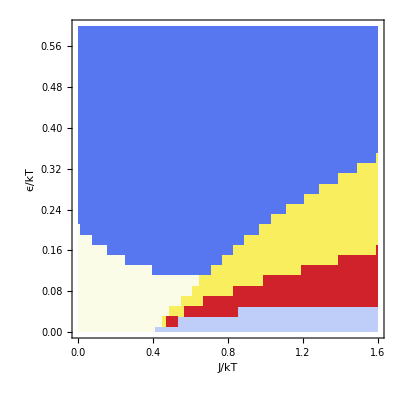

```mathematica
map2=ListContourPlot[mapShort,PlotLegends->None,InterpolationOrder -> 0,FrameLabel->{"J/kT","ϵ/kT"},ColorFunction->"TemperatureMap",Contours->{1,2,3,4,5},ContourStyle->None,BaseStyle->{FontSize->14},Epilog->Inset[Framed[SwatchLegend["TemperatureMap",{"One peak at N=0","One peak at N=L","One peak elsewhere","Two peaks, first larger","Two peaks, second larger"}],Background->White],{0.6,0.47}]]
```

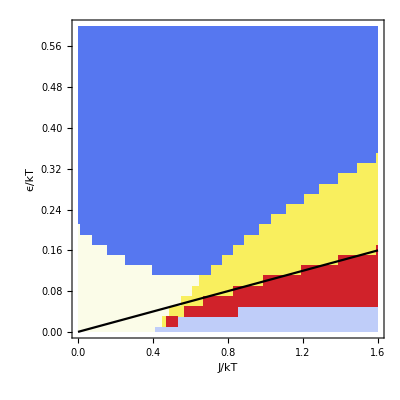

```mathematica
fig4=Show[map2,line]
```

```mathematica
Export["/Users/rachelkrueger/Documents/StatMech/fig4.eps",fig4]
```

/Users/rachelkrueger/Documents/StatMech/fig4.eps